# Electric Potential & Field

## Lab Report

Names: Andrew Bassett & Aryan Malhotra
Section: H5
Date: 2/25/2025

## Purpose

To map the electric potential of different shapes of charged conductors, and compute the corresponding electric fields from these maps.

## Apparatus

DC power supply, multimeter, three field map boards.

## Readings

### Electric Field & Electric Potential

The electric vector field E at a point is the force per unit charge on a test charge located at that point. It is numerically equal to the force on a unit (one Coulomb) positive test charge. Because similar charges repel each other, a positive test charge placed near another positive charge experiences a repulsive force, and the field due to a positive charge points away from the charge. The field direction near a negative charged object is towards the object.

Electric-Field Lines:
Electric field lines are a way of visualizing the electric field near charged objects. Field lines define the direction of the force that a positive “test” charge experiences near other charges. The field lines are also used to define the magnitude of the electric field. The lines are drawn such that their density (the number of lines that cross a unit area) is proportional to the magnitude of E.

Rather than trying to measure electric fields directly, it is easier to measure the electrical potential near the charges. This is an easier measurement because electric potential does not have a direction (it’s a scalar) and can be measured with a voltmeter.

Equipotential Lines:
Consider a test charge that is made to move in the presence of one or more other charges in such a direction that it does not experience any change in electrical potential energy. The path of this test charge is perpendicular to the electric field at every point of its motion, and is called an equipotential line. No work is done to move the test charge; its potential energy does not change.  We define electrical potential as the electrical potential energy divided by the test charge. The unit of electrical potential is the Volt. Work against the electric field happens only when the charge is moved with a component parallel to the E field; thus, equipotential lines are perpendicular to the E field.  Devices that measure electric potential are voltmeters, which are inexpensive and readily available. The equipotential lines, V, measured with the voltmeter can then be used to map the electric field lines, E.

From the definitions of E and V it follows that:
• Electric field lines at any location are perpendicular to the equipotential lines.
• Electric field lines are directed from higher to lower potential.
• Electric fields are vectors: they define the direction of force on test charge.

Some properties of electrically charged conductors in electrostatic equilibrium:
• All points on the conductor's surface are at the same potential.
• The electric field at a conductor's surface is perpendicular at each point to the surface (since the entire conductor surface is at the same potential).
• The electric field at the surface of a charged conductor is large at a sharp point (a convex region with small radius of curvature).

Example 1:
Consider the point P near the positive charge in Figure 1. The electric field lines and the associated equipotential lines are shown. At point P you measure E  = 40 N/C pointing to the right and V = +200V. What do these quantities mean? If a charge of +1.0 nanocoulomb (1 nC = 10^-9 C) is brought to this point, the electric force on the charge is F_e=q E =1.0×10^-9C × 40 N/C to the right=4.0×10^-8N to the right.
The value of the electric potential, V = +200 V, means that the work required to bring a charge of +1.0 x10^-9 C from the location where the electric potential is zero up to 200 V is W=q V=1.0×10^-9C×200 J/C=+2.0×10^-7J.
An electric field can be expressed in units of Volts per meter, as well as in units of Newtons per Coulomb. The field can be written as E = 40 N/C = 40 V/m to the right. This means that if you make a small 1 cm displacement along the direction of E, the electric potential drops by 0.40 volt, from 200.0 V to 199.6 V. In general, E= -\[Laplacian]V/\[Laplacian]s, where \[Laplacian]s is a small displacement along the direction of E and \[Laplacian]V is the corresponding change in electric potential; the minus sign means that V drops along the direction of E.

Figure 1. Example 1, the electric field lines and the equipotential lines for a positive point charge, on the 2D plane. 

-Graphics-

Calculating Electric Potential:
In class you have learned that the potential due to a number of charges can be found by adding up the potential at the point of interest due to each charge. In two dimensions (a plane in three dimensions) this can be written as,
(1)	V(x_P,y_P)=1/(4 πϵ_0)∑_i Q_i/(√((x_i-x_P)^2+(y_i-y_P)^2)),
where V(x_P,y_P) means the potential at the point (x_(P,)y_P) and (x_i,y_i) is the location of the charge Q_i. This is simply Coulomb’s law expressed in terms of potential rather than electric field.

### Subtleties of Experimental Setup (Optional)

(You need to understand this part to answer the optional questions.)
In today's experiment, we will use two-dimensional sheet of conducting material and use DC electric current to generate the potential maps. So there are few subtleties here,
A. The experiment is done using DC currents and potential, rather than actual electrostatic charges.
B. The space is two-dimensional, because the current only flows on the plane.
C. Boundaries.
Here, we explain these subtleties and few ways to think about them.

A. Using DC Current
The mathematical description of conductors having DC currents between them in a uniform isotropic resistivity is exactly the same as the electrostatics equations. The only difference is that now you have both current and electric field at each point and they are related by a simple equation,
(5)	E=ρ J,
where ρ is a constant which is called resistivity and J is the current density (it is a vector field that shows how much charges are passing per unit time per unit area in a direction). So the electric field lines also show the current lines, i.e. how the charge flows.

B. Space is 2D
Doing the actual three dimensional electrostatics experiment is almost impossible with a simple setup. So instead we are using DC currents to simulate the electrostatics situation. See A above. Now again, doing DC current experiments in a three dimensional bulk in a way that we can measure the voltages inside this bulk is tricky (unless we were living in four dimensional space). So we do the DC current experiment on a two dimensional plane so we can access the different points on it and measure their voltages.
To think about the two-dimensional plane, you can extend it to three dimensions (x,y,z) in a way that no observable depends on the third axis value, i.e. z.
This means, for example, if you have two points on the two-dimensional plane, you can think about two rods perpendicular to the plane, i.e. parallel to the z-axis. So the actual potential that you will be measuring is actually the potential given by these infinitely long parallel rods. It is rather easy to find the electric field using the Gauss's law and calculate the electric potential integrating the electric field. For an infinitely long rod what you get is 1/r function for the electric field and the log function for the potential,
(2)	E_r=λ/(2 πϵ_0)1/r,	V=λ/(2 πϵ_0)ln (r/r_0),
where electric field is only non-zero in radial direction and E_r is the component in the radial direction, λ is the linear charge density on the rod, and r_0 is a reference radius that we set V=0 there.
If you have two rods with opposite charges,
(3)	V=λ/(2 πϵ_0)(ln r_1/r_0-ln r_2/r_0)=λ/(2 πϵ_0)ln r_1/r_2,
(4)	V=constant	⇒	r_1/r_2=constant.
So the equipotential surfaces will be the loci of points which their distance from the two charges has a constant ratio. These are called the Apollonian circles. So theoretically the equipotential lines for two rods (points on two dimensions) are circles. Also the electric field lines are another family of circles perpendicular to equipotential lines.

You will study this example in the part I of the experiment. In part II and III you will use other geometries. The analytical description of those geometries are a bit more difficult. But again, if you want to understand what physically they represent in three dimensions, you need to consider extending them to the third dimension. This means in part II, you are studying the equivalent problem of two infinite strips, and in part III, you are studying the equivalent problem of two infinite strips with an infinite parallel cylinder in the middle.

Of course, this conducting paper, that you use in the experiment, has some width, and in reality you are doing experiment in three dimensions. But effectively and mathematically we can neglect the width and consider the problem to be two dimensional.

Figure 2. Apollonian circles, blue lines are the equipotential lines, and red ones are electric field lines.

-Graphics-

C. Boundaries
Unlike theoretical understanding, which we take the boundaries to be at infinity, here in the experiment we are dealing with a finite piece of paper. So the boundary conditions on the edges of this paper will contribute substantially to what we observe. The way to understand these boundaries is that the electric field (or the current) at these boundaries are parallel to the boundary, or in other words normal part of the electric field (or current) becomes zero at the boundary. The reason is that no current can flow out of the paper. In math jargon, this is known as a Neumann boundary condition for the potential. Unlike the boundary conditions on the electrodes, which fixes the value of the voltage at those points (known as Dirichlet boundary condition), the condition on edge fixes the derivative of the voltage normal to the boundary to zero.

## Procedure

You will measure electric potential and draw equipotential lines for three different configurations of oppositely charged conductors:
1. two points;
2. two parallel plates (a capacitor);
3. a hollow circular conductor between oppositely charged parallel plates.

Figure 3 shows the experimental arrangement for simulating the electric field between two point charges. A dc power supply set just under 20 volts is connected across the two conductors. A digital multimeter set to read DC voltage on the 20 V scale (if the applied voltage exceeds 20 V the DMM will always read 1) and has its negative lead fixed to the negative electrode; the positive meter lead may be touched to any point on the high- resistance conducting sheet (centimeter grid) to measure the electric potential at that point.

Electric charges flow from one electrode to the other through the conducting sheet; this situation simulates very closely that of two charged electrodes (rods perpendicular to surface of the board) in electrostatic equilibrium (Side note for interested reader: Both are solving Laplace partial differential equation in two dimensions with Dirichlet boundary conditions on the conductors.).

For each configuration you will locate and plot some equipotential lines. All points of one conductor are at 0V; all points of the other at (just under) +20V. Check it! Indicate on the field plot the polarity of each electrode, + or -.
The potential is measured on the black conducting sheet; the data are to be entered on this notebook. You will measure the voltage at each one cm grid point, so you will have a 21x29 matrix at the end for each part.

For the parallel strip electrodes measure potential beyond and to the sides of the electrode region.  For the circular electrode between parallel strips make measurements inside the ring to test shielding. For the two points electrode configuration, measure behind the points as well as between, to map the dipole (two-pole) shape.

To simplify plotting it is a good idea to scan along straight centimeter grid lines. Since each configuration is symmetrical, it will be sufficient to measure one side and to sketch the other side symmetrically. So for part I you will measure the top side, and for parts II and III you will measure the left side.

Connect points at the same potential with smooth lines to produce equipotential lines. Label the potentials.  Show the associated electric-field vector at several locations.  The E field lines should be everywhere perpendicular to the equipotential lines, from the defining relation between E and V.  The direction of E is toward decreasing potential V.  Show the direction of the E field lines on your plot.

Figure 3. The setup of the experiment (for part I board).

-Graphics-

Warnings:
- Touch with the probe; don’t gouge the black paper.
- PLEASE do not write on or scratch the paper. Replacement is very costly.

## Dialog:

## Part I. Two Opposite Point Charges

### Step 1. Measurements

- Measure the voltage only on the grid points and insert the voltage data on the table below. There are 29 columns and 11 rows. 1st row is the top of the page, and 11th row is where the screws are sitting at. So we are doing upper half of the page only. Because of symmetry the bottom half will be the same. The ? shows the power source voltage.

If the screws are not on the correct row and shifted half a row above, you can measure 10 rows instead of 11 below.

```mathematica
Vgrid={{5.91, 5.94, 6, 6.07, 6.2, 6.32, 6.42, 6.71, 7, 7.39, 7.74, 8.1, 8.53, 9.09, 9.6, 10.17, 10.65, 11.05, 11.41, 11.74, 11.97, 12.23, 12.41, 12.53, 12.64, 12.72, 12.77}, {5.81, 5.84, 5.92, 5.96, 6.08, 6.21, 6.33, 6.61, 6.96, 7.33, 7.71, 8.11, 8.61, 9.11, 9.63, 10.19, 10.73, 11.12, 11.5, 11.84, 12.11, 12.32, 12.52, 12.65, 12.76, 12.81, 12.84}, {5.65, 5.7, 5.74, 5.80, 5.93, 6.06, 6.17, 6.46, 6.87, 7.25, 7.65, 8.09, 8.59, 9.18, 9.73, 10.34, 10.88, 11.27, 11.63, 12.05, 12.26, 12.49, 12.64, 12.78, 12.83, 12.9, 12.92}, {5.53, 5.56, 5.6, 5.62, 5.74, 5.85, 5.95, 6.27, 6.62, 7.03, 7.5, 7.98, 8.54, 9.16, 9.89, 10.49, 11.1, 11.49, 12.05, 12.36, 12.58, 12.76, 12.87, 12.97, 13.02, 13.04, 13.04}, {5.39, 5.41, 5.42, 5.43, 5.43, 5.6, 5.59, 5.95, 6.3, 6.75, 7.25, 7.83, 8.53, 9.22, 10.02, 10.62, 11.41, 11.588, 12.42, 12.74, 12.93, 13.06, 13.12, 13.18, 13.17, 13.2, 13.2}, {5.27, 5.27, 5.25, 5.21, 5.22, 5.28, 5.29, 5.57, 5.9, 6.39, 6.94, 7.67, 8.4, 9.21, 10.07, 10.9, 11.84, 12.38, 12.87, 13.26, 13.42, 13.44, 13.41, 12.39, 13.38, 13.35, 13.33}, {5.15, 5.14, 5.08, 4.99, 4.92, 4.85, 4.76, 5, 5.4, 5.91, 6.56, 7.31, 8.18, 9.22, 10.32, 11.14, 12.26, 13.15, 13.8, 13.89, 13.89, 13.83, 13.68, 13.61, 13.53, 13.52, 13.47}, {5.07, 5.02, 4.93, 4.79, 4.64, 4.4, 4.18, 4.13, 4.51, 5.1, 5.92, 6.95, 8.03, 9.17, 10.39, 11.71, 12.96, 14.07, 14.79, 14.78, 14.58, 14.22, 13.98, 13.81, 13.69, 13.62, 13.55}, {5, 4.94, 4.85, 4.67, 4.45, 4.04, 3.57, 3.12, 2.97, 3.91, 5.44, 6.6, 7.9, 9.25, 10.56, 11.8, 13.55, 15.26, 16.28, 15.87, 15.16, 14.56, 14.19, 13.94, 13.79, 13.68, 13.61}, {4.98, 4.93, 4.82, 4.66, 4.37, 3.98, 3.17, 1.63, 0.00, 2.4, 4.83, 6.48, 7.92, 9.2, 10.48, 12, 13.7, 16.54, 18.91, 16.94, 15.45, 14.74, 14.3, 13.99, 13.8, 13.69, 13.6}}; 
(* Now this line of code, copies all the rows in reverse order (mirror symmetry) to fill out the whole page. 12th row is the same as 10th row and so on. *)
nrows = Dimensions[Vgrid][[1]]; (* 11 or 10 *)
ncols = Dimensions[Vgrid][[2]]; (* 29 *)
sheetHLength=ncols; (* Sheet horizontal length. 29. *)
sheetVLength=2*nrows-1; (* Sheet vertical length. 21 or 19. *)

For[i=nrows-1,i>0,i--,Vgrid =Append[Vgrid,Vgrid[[i,All]]];]; 

(* This chunk of code, makes an interpolation using the data. *)
VgridTr =Transpose[Vgrid]; (* To make row number y and column number x. *)
(* VgridSmooth can be used as a function of [x,y]. It is an interpolation over the data. *)
VgridSmooth=Interpolation[Flatten[Array[{{#1,#2},VgridTr[[#1,#2]]}&,{sheetHLength,sheetVLength}],1]];

(* V is the maximum voltage which is the power source voltage, about 20V.*)
V = Max[Vgrid];
Print["Power Source Voltage = V = ", V, " ± 0.01 Volts"]
```

Power Source Voltage = V = 18.91 ± 0.01 Volts

#### Question 1. - By measuring few points and their points on the other side, estimate the percentage of error we introduced by assuming that the potential is symmetric with respect to the middle line.

#### Answer 1. - By picking 10 random points on the other side of the grid and comparing them to the value of the mirrored points corresponding to the side of grid that we measured our potentials for, we can estimate the error. Since we assume that the arrangement is symmetrical, both the voltages for the point and mirrored points must be the same. The following were the points we measured corresponding to their mirrored points in our grid: 11.12 | 10.01 4.66 | 4.82 5.85 | 5.43 13.61 | 14.0 12.76 | 12.58 5.15 | 5.0 7.71 | 7.87 11.63 | 11.89 9.73 | 9.57 5.8 | 6.33 would thus be the average fractional error in our measurement with the symmetric configuration assumption. Hence, the percentage error is the fractional error multiplied by 100, which turns out to be 4.2%. Therefore, the assumption of having a symmetrical distribution is a reasonable assumption.

### Step 2. Plotting & Analysis

- Now plot the electric potential in x-y plane. Also plot the equipotential lines and electric field lines. To draw the electric field lines we are using StreamPlot function with the derivative of the potential.
- Answer the questions.

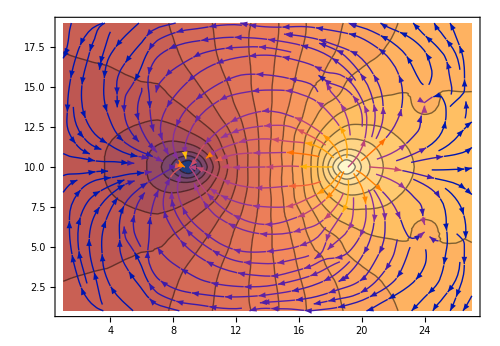
-Graphics3D--Graphics-

```mathematica
f = VgridSmooth;
pot=Plot3D[f[x,y],{x,1,sheetHLength},{y,1,sheetVLength},MeshFunctions->{#3&},Mesh->14,FaceGrids->All];
vf=StreamPlot[Evaluate[-D[f[x,y],{{x,y}}]],{x,1,sheetHLength},{y,1,sheetVLength},StreamStyle->ColorData[1][3]];
cp=Show[ContourPlot[f[x,y],{x,1,sheetHLength},{y,1,sheetVLength},Contours->{V/20,2V/20,3V/20,4V/20,5V/20,6V/20,7V/20,8V/20,9V/20,V/2,11V/20,12V/20,13V/20,14V/20,15V/20,16V/20,17V/20,18V/20,19V/20}
],vf];
Row[{Show[pot,ImageSize->500],Show[cp,ImageSize->500,AspectRatio->Automatic]}]
```

#### Question 2. - Where is E most nearly uniform? - Describe the shape of the central equipotential line near the midpoint of the conductors. - What is the equipotential shape close to the “point” electrodes? - Estimate the electric field (magnitude and direction) and its error at the center of the sheet. (Create an input cell and use the variable ECi and the Around function) - The potential is everywhere the same on an equipotential line. Is the electric field everywhere the same on an electric field line?

#### Answer 2. - E is most nearly uniform along the line that connects the two screws, both between them , this is where the density of the Electric field lines remains the same. This is also where the Voltage has a nearly constant slope (Hence, E field bring it’s gradient, it must be constant) - Near the midpoint, the perpendicular bisector of the line joining the two poles is the equipotential line which is approximately straight, this makes sense because points here are equidistant from both the poles of charge, hence the potential at this point must cancel. Also, equipotential line must be perpendicular to the fields at the centre which are totally horizontal. - The equipotential lines wrap around the charges in a circle, which (assuming they are point charges) is correct as they would then be perpendicular to all the fields emanating radially from the point. - The working has been shown in the code block below. We took the 3 middle rows to get the 3x3 grid of the central grid-points and averaged over the extreme values. □ | V5[6] | □ V6[5] | Centre | V6[7] □ | V7[6] | □ (The bottom row is an extrapolation by symmetric arguments of the top row) So avgEx = -avg(Vx)/avg(d) =-avg(V6[7]-V6[5])/2cm = -128 N/C Similarly, avgEy = - avg(Vy)/avg(d) = -avg(V5[6]-V7[6])/2cm = 0 N/C (since of course, our data is assumed to be symmetric) Considering the errors in the symmetric assumption (4.2% as estimated earlier) and a 1mm variation in the gridpoints, the net E field is (-128.00±0.07,0.±19.)N/C (vectorially) Hence, the magnitude of the E field is 128.00±0.10 N/C Primarily, the E field is in the negative x direction (towards the lower potential). - Electric fie.08lds magnitude is totally blind to where exactly on the line you are. For field lines, the magnitude of the field is determined by the density of the field lines in a given region. Usually, moving further away from the charge source gets the density lowered overall, hence, E field along the lines would decrease.

```mathematica
(*Define rows Volts*)
V5={2.97,3.91,5.44,6.6,7.9,9.25,10.56,11.8,13.55,15.26,16.28};
V6={0.00,2.4,4.83,6.48,7.92,9.2,10.48,12,13.7,16.54,18.91};
V7=V5;  (*Symmetry assumption*)

(*Spacing m*)
δx=0.01;δy=0.01;

(*Electric field components at center,column 6*)
ECi={Around[-(V6[[7]]-V6[[5]])/(2 δx),Sqrt[0.001^2+0.001^2]/(2 δx)],Around[-(V7[[6]]-V5[[6]])/(2 δy),Sqrt[(0.042*V7[[6]])^2+0.001^2]/(2 δy)]}; (*Accounting for the 4.2% error in Symmetric Assumption*)

(*Magnitude N/C*)
Emag=Around[Sqrt[ECi[[1]]^2+ECi[[2]]^2],Sqrt[(ECi[[1]]*ECi[[1,2]])^2+(ECi[[2]]*ECi[[2,2]])^2]/Sqrt[ECi[[1]]^2+ECi[[2]]^2]];

(*Output*)
{ECi,Emag}
```

{{-128.000.07,0.19.},128.000.10}

### Step 3. Further Analysis (Optional)

Theoretically, as we discussed above, the equipotential lines and field lines are circles.
- Explain how the experimental result is different from the theoretical prediction and what causes this disagreement.
- Plot the region that the theory and experiment have much better match and explain why. You only need to change the x and y axis ranges on the above code.
- Using the data, integrate the current coming out of an electrode and find the total current. Compare this value to the current you can read from the DC source screen (ammeter).

Answer:
Put your work here.

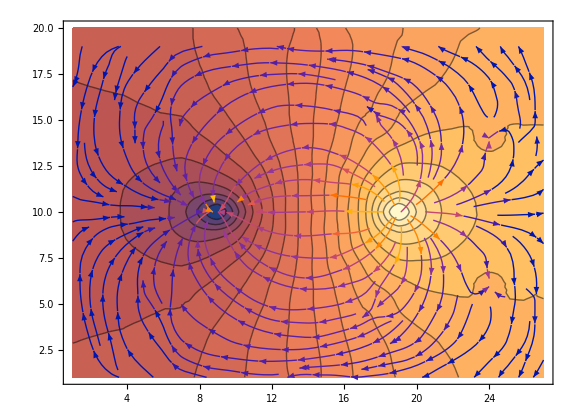

```mathematica
(* This is an Input cell in case you need *)
Show[
ContourPlot[f[x,y],{x,1,27},{y,1,20},
Contours->{V/20,2V/20,3V/20,4V/20,5V/20,6V/20,7V/20,8V/20,9V/20,V/2,11V/20,12V/20,13V/20,14V/20,15V/20,16V/20,17V/20,18V/20,19V/20}],vf, AspectRatio->Automatic,ImageSize->Large]
```

## Part II. Two Parallel Plates

### Step 1. Measurements

- Similar to the part I, measure the voltages at each point on the grid (spaced by 1 cm). This time you are measuring the left side of the page. The right side will be symmetric.

```mathematica
Vgrid2={{14.93, 15.07, 15.2, 15.4, 15.63, 15.99, 16.2, 16.54, 16.84, 17.09, 17.27, 17.45, 17.55, 17.59, 17.6}, {14.73, 14.85, 15.02, 15.23, 15.52, 15.92, 16.22, 16.63, 16.94, 17.24, 17.44, 17.56, 17.66, 17.70, 17.70}, {14.47, 14.57, 14.78, 15, 15.37, 15.84, 16.22, 16.77, 17.14, 17.45, 17.65, 17.75, 17.81, 17.86, 17.86}, {14.05, 14.2, 14.45, 14.7, 14.99, 15.69, 16.23, 17, 17.57, 17.79, 17.62, 17.99, 18.03, 18.05, 18.03}, {13.59, 13.69, 14, 14.2, 14.4, 15.4, 16.18, V, V, V, V, V, V, V, V}, {12.96, 13.14, 13.35, 13.57, 13.6, 14.77, 15.68, V, V, V, V, V, V, V, V}, {12.13, 12.28, 12.41, 12.66, 12.83, 13.7, 14.37, 15.13, 15.42, 15.98, 16.07, 16.2, 16.19, 16.16, 16.3}, {11.11, 11.29, 11.26, 11.42, 11.46, 12.17, 12.64, 13.06, 13.51, 13.69, 13.88, 14.06, 14.05, 14.01, 14.06}, {9.98, 10.02, 10.16, 10.27, 10.28, 10.9, 10.86, 11.13, 11.37, 11.56, 11.67, 11.81, 11.96, 12.1, 12.10}, {9.18, 9.03, 8.98, 9.22, 9.08, 9.36, 9.28, 9.64, 9.69, 9.91, 9.9, 9.92, 9.9, 10.13, 10.04}, {8.12, 8.16, 8.29, 8.04, 7.9, 7.76, 7.62, 7.69, 7.55, 7.69, 7.82, 7.85, 7.92, 7.91, 7.89}, {7.31, 7.39, 7.02, 6.9, 6.55, 6.3, 6, 5.63, 5.68, 5.66, 7.56, 5.81, 5.81, 5.83, 5.98}, {6.44, 6.23, 6.14, 5.82, 5.28, 5.01, 4.36, 3.87, 3.51, 3.52, 3.49, 3.49, 3.62, 3.45, 3.74}, {5.59, 5.47, 5.26, 4.94, 5.33, 3.99, 2.92, 0, 0, 0, 0, 0, 0, 0, 0}, {4.93, 4.83, 4.62, 4.22, 3.78, 3.2, 2.35, 0, 0, 0, 0, 0, 0, 0, 0}, {4.36, 4.24, 4.06, 3.63, 3.26, 2.86, 2.09, 1.26, 0.8, 0.57, 0.4, 0.35, 0.31, 0.32, 0.3}, {3.7, 3.73, 3.59, 3.29, 2.87, 2.56, 2.06, 1.61, 1.25, 0.97, 0.74, 0.65, 0.61, 0.59, 0.61}, {3.53, 3.42, 3.26, 3.02, 2.71, 2.43, 2.03, 1.76, 1.44, 1.21, 0.99, 0.9, 0.84, 0.8, 0.8}, {3.3, 3.2, 3.09, 2.86, 2.62, 2.35, 2.08, 1.8, 1.57, 1.36, 1.17, 1.05, 0.97, 0.93, 0.93}, {3.15, 3.07, 2.94, 2.75, 2.51, 2.27, 2.07, 1.87, 1.67, 1.45, 1.28, 1.16, 1.06, 1.02, 1.02}, {3.05, 2.98, 2.88, 2.67, 2.45, 2.29, 2.04, 1.9, 1.7, 1.49, 1.32, 1.21, 1.11, 1.08, 1.07}};
(* Now this chunk of code, copies all the columns in reverse order (mirror symmetry) to fill out the whole page. 16th column is the same as 14th column and so on. *)
For[j=14,j>0,j--,
column = Vgrid2[[All, j]];
Vgrid2=MapThread[Insert,{Vgrid2,column,Table[30-j,{Length[column]}]}] ;
]

(* This chunk of code, makes an interpolation using the data. *)
Vgrid2Tr =Transpose[Vgrid2]; (* To make row number y and column number x. *)
(* Vgrid2Smooth can be used as a function of [x,y]. It is an interpolation over the data. *)
Vgrid2Smooth=Interpolation[Flatten[Array[{{#1,#2},Vgrid2Tr[[#1,#2]]}&,{29,21}],1]];
```

### Step 2. Plotting & Analysis

- Again, we plot the potential, equipotential lines, and electric field lines.

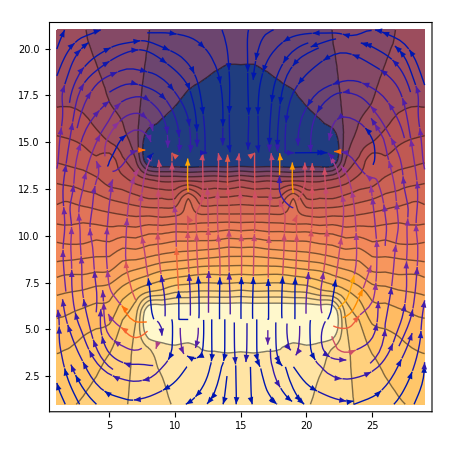
-Graphics3D--Graphics-

```mathematica
f = Vgrid2Smooth;
pot=Plot3D[f[x,y],{x,1,29},{y,1,21},MeshFunctions->{#3&},Mesh->14,FaceGrids->All];
vf=StreamPlot[Evaluate[-D[f[x,y],{{x,y}}]],{x,1,29},{y,1,21},StreamStyle->ColorData[1][3]];
cp=Show[ContourPlot[f[x,y],{x,1,29},{y,1,21},Contours->{V/20,2V/20,3V/20,4V/20,5V/20,6V/20,7V/20,8V/20,9V/20,V/2,11V/20,12V/20,13V/20,14V/20,15V/20,16V/20,17V/20,18V/20,19V/20}
],vf];
Row[{Show[pot,ImageSize->500],Show[cp,ImageSize->450]}]
```

#### Question 3. - Describe the shape of E ​in between the plates. Where is E most nearly uniform? - Does E ​extend beyond the edges of the plates? - Estimate the electric field (magnitude and direction) and its error at the center of the sheet. (Create an input cell and use the variable ECii and the Around function) - Compare the above electric field to the electric field of a large parallel plate capacitor with the same voltage and distance between the plates. Which one is larger? Is this expected? Explain.

#### Answer 3. - Between the plates the electric field mostly is straight and linear. It is most uniform at the very center of the plates. - Yes the E field extends beyond the edges of the plate. Beyond the plates however, the electric field is much weaker than in between but it still exists! It makes sense because we do not have an infinite plane of charge hence there are boundary effects that cause these fields. - Again here are the Voltage values at the centre: □ | 10.13 | □ 12.10 | Centre | 7.89 □ | 10.13 | □ (The right column here has been an extrapolation of the left column by a symmetrical argument) Like before, avgEx = -avg(Vx)/avg(d) =-avg(VC3[2]-V1[2])/2cm = 0 N/C Similarly, avgEy = - avg(Vy)/avg(d) = -avg(VC3[3]-VC1[1])/2cm = 246 N/C (since of course, our data is assumed to be symmetric) Considering the errors in the symmetric assumption (4.2% as estimated earlier) and a 1mm variation in the gridpoints, the net E field is (0.00±0.07,246.±25.)N/C (vectorially) Hence, the magnitude of the E field is 246.00±36. N/C Primarily, the E field is in the positive y direction (towards the lower potential). -

```mathematica
(*Define voltages*)
VC1={12.1,10.13,7.19};  (*Left,column 13*)
VC2={12.10,10.04,7.89};  (*Middle,column 14*)
VC3=VC1;  (*Right,column 15,symmetric*)

(*Spacing in meters*)
δx=0.01;δy=0.01;

(*Electric field components at center,column 14,row 2*)
ECiii={Around[-(VC3[[2]]-VC1[[2]])/(2 δx),Sqrt[0.001^2+0.001^2]/(2 δx)],Around[-(VC3[[3]]-VC1[[1]])/(2 δy),Sqrt[(0.042*VC3[[1]])^2+0.001^2]/(2 δy)]};

(*Magnitude*)
Emag=Around[Sqrt[ECiii[[1]]^2+ECiii[[2]]^2],Sqrt[(ECiii[[1]]*ECiii[[1,2]])^2+(ECiii[[2]]*ECiii[[2,2]])^2]/Sqrt[ECiii[[1]]^2+ECiii[[2]]^2]];

(*Output*)
{ECiii,Emag}
```

{{0.000.07,246.25.},246.36.}

## Part III. Hollow Circular Conductor Between Parallel Plates

### Step 1. Measurements

```mathematica
Vgrid3={{17.36, 17.61, 18.01, 18.44, 18.63, 18.65, 18.67, 18.63, 18.57, 18.61, 18.61, 18.54, 18.56, 18.57, 18.52}, {17.10, 17.40, 17.85, V, V, V, V, V, V, V, V, V, V, V, V}, {16.68, 16.84, 17.30, V, V, V, V, V, V, V, V, V, V, V, V}, {15.83, 15.98, 16.33, 16.56, 16.79, 16.95, 16.82, 16.76, 16.67, 16.46, 16.30, 16.21, 16.3, 16.22, 16.08}, {14.93, 15.02, 15.14, 15.26, 15.34, 15.38, 15.36, 15.12, 14.84, 14.61, 14.38, 13.93, 13.95, 13.55, 13.59}, {14.01, 13.95, 14, 14.09, 14.20, 13.99, 13.96, 13.75, 13.51, 13.05, 12.66, 12.15, 11.63, 11.22, 11.49}, {13.8, 13.22, 13.02, 13.04, 13.09, 12.89, 12.88, 12.58, 12.27, 11.93, 11.21, 10.41, 9.14, 9.13, 9.14}, {12.27, 12.17, 12.17, 12.14, 12.12, 11.84, 11.77, 11.56, 11.36, 10.86, 10.01, 9.13, 9.14, 9.22, 9.18}, {11.15, 11.18, 11.11, 11.06, 10.97, 10.77, 10.76, 10.58, 10.36, 10, 9.13, 9.13, 9.18, 9.18, 9.20}, {10.27, 10.27, 10.15, 10.06, 10.05, 9.92, 9.89, 9.84, 9.63, 9.47, 9.13, 9.22, 9.18, 9.17, 9.18}, {9.19, 9.26, 9.17, 9.10, 9.07, 9.08, 8.98, 9, 8.99, 9.06, 9.13, 9.14, 9.14, 9.14, 9.14}, {8.35, 8.29, 8.09, 8.18, 8.18, 8.23, 8.20, 8.32, 8.49, 8.69, 9.13, 9.08, 9.11, 9.11, 9.12}, {6.89, 7.03, 7.08, 7.18, 7.21, 7.31, 7.39, 7.56, 7.88, 8.31, 9.13, 9.15, 9.10, 9.09, 9.10}, {6.6, 6.06, 6.11, 6.20, 6.20, 6.52, 6.53, 6.83, 7.04, 7.53, 8.18, 9.14, 9.15, 9.05, 9.09}, {5.25, 5.22, 5.2, 5.33, 5.32, 5.65, 5.70, 5.98, 6.20, 6.60, 7.16, 7.75, 9.14, 9.15, 9.14}, {4.32, 4.15, 4.29, 4.37, 4.47, 4.80, 4.80, 4.98, 5.15, 5.45, 5.72, 6.31, 6.62, 7, 7.37}, {3.27, 3.04, 3.2, 3.37, 3.28, 3.57, 3.51, 3.85, 4.19, 4.27, 4.39, 4.78, 4.87, 4.98, 5.14}, {2.38, 2.32, 2, 2, 1.89, 2.27, 2.18, 2.52, 2.8, 3, 3.05, 3.06, 2.69, 3, 2.82}, {1.83, 1.60, 1.13, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1.3, 1.07, 0.68, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1.04, 0.89, 0.66, 0.47, 0.46, 0.63, 0.84, 1.02, 1.13, 1.13, 1.07, 0.84, 0.57, 0.41, 0.4}};
(* Now this chunk of code, copies all the columns in reverse order (mirror symmetry) to fill out the whole page. 16th column is the same as 14th column and so on. *)
For[j=14,j>0,j--,
column = Vgrid3[[All, j]];
Vgrid3=MapThread[Insert,{Vgrid3,column,Table[30-j,{Length[column]}]}] ;
]

(* This chunk of code, makes an interpolation using the data. *)
Vgrid3Tr =Transpose[Vgrid3]; (* To make row number y and column number x. *)
(* Vgrid3Smooth can be used as a function of [x,y]. It is an interpolation over the data. *)
Vgrid3Smooth=Interpolation[Flatten[Array[{{#1,#2},Vgrid3Tr[[#1,#2]]}&,{29,21}],1]];
```

### Step 2. Plotting & Analysis

- Again, we plot the potential, equipotential lines, and electric field lines.

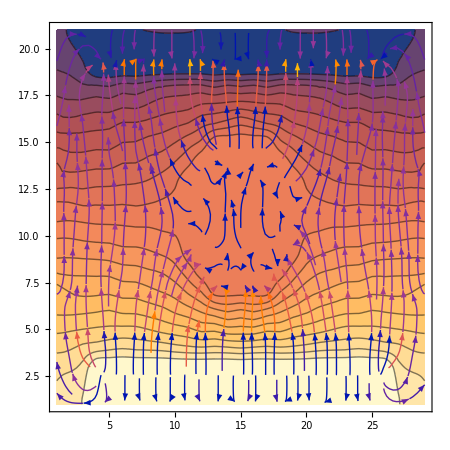
-Graphics3D--Graphics-

```mathematica
f = Vgrid3Smooth;
pot=Plot3D[f[x,y],{x,1,29},{y,1,21},MeshFunctions->{#3&},Mesh->14,FaceGrids->All];
vf=StreamPlot[Evaluate[-D[f[x,y],{{x,y}}]],{x,1,29},{y,1,21},StreamStyle->ColorData[1][3]];
cp=Show[ContourPlot[f[x,y],{x,1,29},{y,1,21},Contours->{V/20,2V/20,3V/20,4V/20,5V/20,6V/20,7V/20,8V/20,9V/20,V/2,11V/20,12V/20,13V/20,14V/20,15V/20,16V/20,17V/20,18V/20,19V/20}
],vf];
Row[{Show[pot,ImageSize->500],Show[cp,ImageSize->450]}]
```

#### Question 4. - Is there a net charge on the circular conductor? Give an argument based on the shape of the electric field and the equipotential lines. - What is V on the conductor ring? What is V inside the ring? (Create an input cell and use the variable Vcircle and the Around function) - What should E ​be inside the conducting circle? Is the inside of the circle “shielded” from electric field as expected? Why or why not?

#### Answer 4. - the field lines point away from the circular conductor and away at others, were there a charge, either postive or negative, on the conductor, the field lines would have to be attracted to or repelled by it. - -

```mathematica
(*Define the voltage lists for points on and inside the ring (left side)*)VringLeft={{9.13,9.13,9.13,9.13,9.13},{9.13,9.13,9.22,9.14,9.08,9.15,9.14},{9.14,9.14,9.18,9.18,9.14,9.11,9.10,9.15,9.14},{9.13,9.22,9.18,9.17,9.14,9.11,9.09,9.05,9.15},{9.14,9.18,9.20,9.18,9.14,9.12,9.10,9.09,9.14}};

(*Flatten the list and calculate the mean*)
Vflat=Flatten[VringLeft];

(*Voltage on the ring and inside,with measurement uncertainty*)
Vcircle=Around[Vflat];

(*Output*)
Vcircle
```

9.140.04

### Table X. Copy All Your Final Results.

```mathematica
Grid[{{Text["Table X. All Final Results Gathered"],SpanFromLeft},
{"E_C^I [Part I] (V/m)","E_C^II [Part II] (V/m)","V_circle (V)"},
{ECi,
ECii,
Vcircle}
},Frame->All]
```

Table X. All Final Results Gathered |  | 
E_C^I [Part I] (V/m) | E_C^II [Part II] (V/m) | V_circle (V)
ECi | ECii | Vcircle

Rutgers 276 Classical Physics Lab
“Electric Potential & Field”
Copyright 2017 Roshan Tourani and Girsh Blumberg